```mathematica
(* Make this notebook standalone *)
(* See: http://stackoverflow.com/questions/4896011/mathematica-separating-notebooks *)
SetOptions[EvaluationNotebook[], CellContext -> Notebook]
```

```mathematica
(* 

All of this is from 

Smith,Steven B.,Yujia Cui,and Carlos Bustamente.“Overstretching B-DNA:The Elastic Response of Individual Double-Stranded and Single-Stranded DNA Molecules.” Science 271,no.5250 (February 9,1996):795.
*)
```

```mathematica
Ext[L0_,F_,b_,kbT_,S_]:= L0 * (Coth[F*b/(kbT)] - kbT/(F*b))* (1+F/S)
```

```mathematica
ExtInextensible[L0_,F_,b_,kbT_] := Ext[L0,F,b,kbT,Infinity]
```

```mathematica
(* attempt to reproduce Figure 6, using contour length and Kuhhn specified *)
```

```mathematica
L0 = 27*10^(-6);
```

```mathematica
b = 1.5*10^(-9);
```

```mathematica
S = 800*10^(-12);
```

```mathematica
kbT = 4.1*10^(-21);
```

```mathematica
toMicrons[x_] := x*10^(6)
```

```mathematica
fromPn [x_]:= x * 10^(-12);
```

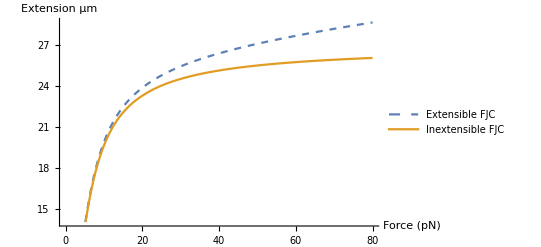

```mathematica
g = Plot[{toMicrons[Ext[L0,fromPn[Force],b,kbT,S]],toMicrons[ExtInextensible[L0,fromPn[Force],b,kbT]]},{Force,0,80},
AxesLabel-> {"Force (pN)","Extension μm"}
,PlotStyle->{Dashed,Thick},PlotLegends->{"Extensible FJC","Inextensible FJC"}]
```

```mathematica
Langevin = Coth[x] -1/x
```

-1/x+Coth[x]

```mathematica
SmallXApprox = Normal[Series[Langevin,{x,0,9}]]
```

x/3-x^3/45+(2 x^5)/945-x^7/4725+(2 x^9)/93555

```mathematica
RelativeError = Abs[Langevin-SmallXApprox]/Min[Langevin,SmallXApprox]
```

Abs[-1/x-x/3+x^3/45-(2 x^5)/945+x^7/4725-(2 x^9)/93555+Coth[x]]/Min[x/3-x^3/45+(2 x^5)/945-x^7/4725+(2 x^9)/93555,-1/x+Coth[x]]

```mathematica
mPlot = LogPlot[{SmallXApprox,Langevin,RelativeError},{x,0,2},
PlotStyle->{Dotted,Dashed},PlotRange->Full,
PlotLegends->{"Small-X Langevin","Exact Langevin","Relative Error"}];
```

```mathematica
choice = ListLogPlot[{{0.2,1*10^(-12)}},PlotLegends->"10^-12 Error below x=0.2"];
```

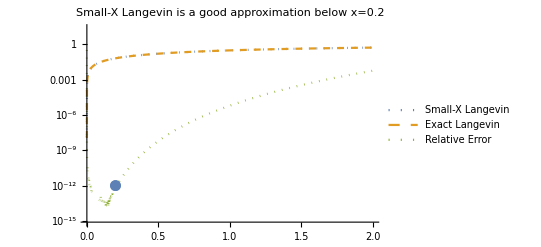

```mathematica
Show[mPlot,choice,PlotLabel-> "Small-X Langevin is a good approximation below x=0.2"]
```